# © Kamal K. Barley, Andreas Ruffing, and Sergei K. Suslov “Oganesson versus Uranium Hydrogen-like Ions from the Viewpoint of Old Quantum Mechanics”

arXiv:2509.06249v2[quant-ph] 11 Sept 2025

https://arxiv.org/pdf/2509.06249

(Last modified/executed on September  24, 2025;  12:30 PM Arizona time.)

```mathematica
SetDirectory[NotebookDirectory[]];
```

0.455419

0.949782

0.0203534

{0.00102211,0.0396847}

7.5133

13.7965

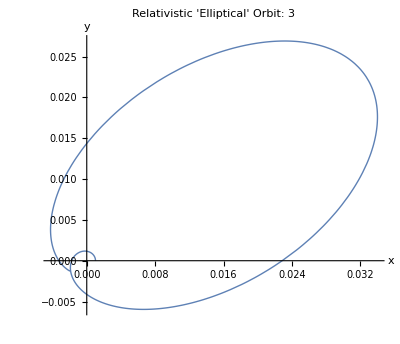

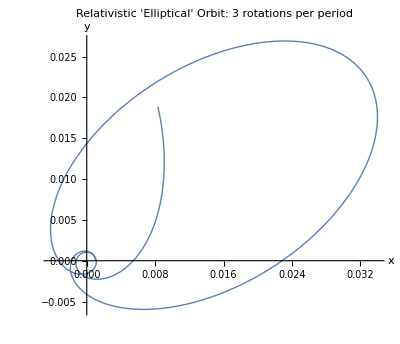

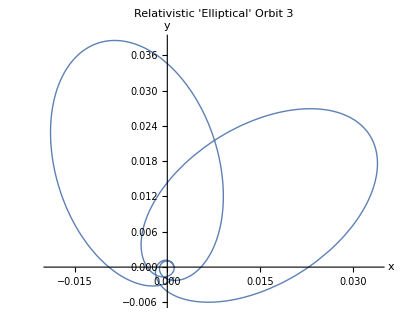

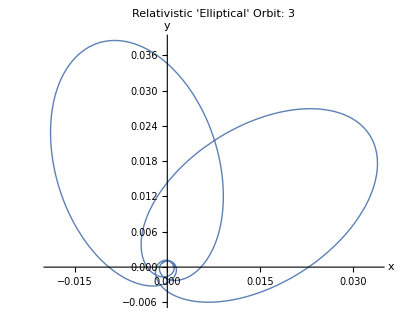

```mathematica
(*---Constants and Setup---*)(*Pretty print subscript-style variables for display only*)MakeBoxes[nt,StandardForm]:=SubscriptBox["n","t"]
MakeBoxes[nr,StandardForm]:=SubscriptBox["n","r"]

(*Physical constants*)
Z=122; (*Atomic number of a hypotetical element Unbibium, Ubb*)
α=1/137.036; (*Fine structure constant*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Define symbolic formulas as functions---*)

(*Eq.(3.19)*)
ωFunc[nt_]:=Sqrt[nt^2-Z^2 α^2]/nt

(*Eq.(3.20)*)
ϵFunc[nt_,nr_]:=Sqrt[nr] Sqrt[(nr+2 Sqrt[nt^2-Z^2 α^2])]/(nr+Sqrt[nt^2-Z^2 α^2])

(*Eq.(3.21)*)
aFunc[nt_,nr_]:=((nr+Sqrt[nt^2-Z^2 α^2]) Sqrt[Z^2 α^2+(nr+Sqrt[nt^2-Z^2 α^2])^2])/Z

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.725*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.45*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.75*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,2*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Export["UnbibiumIon121.pdf",]
```

UnbibiumIon121.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic 'Elliptical' Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min]=0.00102211 to Subscript[r, max]=0.0396847*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,24 Pi,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Unbibium, Ubb, when Z=122, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.455419,  ϵ=0.949782, and a=0.0203534, in Bohr’s atomic units.  The ‘winding’ number is 3!
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.00102211 and r_max=a (1+ϵ)=0.0396847, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=7.5133.  At the point of the first self-intersection one gets, approximately,  r(10.002448573515926)=r(3.7940322175405243)=0.00234067  with  r(10.002448573515926)-r(3.7940322175405243)=0. At the second self-intersection, approximately, r[(6.9329615821129)=r(10.66)=0.0017562 with

```mathematica
0.725*PeriodTheta
```

10.0024

```mathematica
r[10.002448573515926]
```

0.00234067

```mathematica
Solve[ωVal*(10.002448573515926+t)/2-Pi==0,t]
```

{{t→3.79403}}

```mathematica
r[3.794032217540524]
```

0.00234067

```mathematica
10.002448573515926/3.794032217540524
```

2.63636

```mathematica
FindRoot[r[2.636363636363636*t]-r[t],{t,3.7}]
```

{t→3.79403}

```mathematica
2.636363636363636*3.7940322175405243
```

10.0024

```mathematica
r[10.002448573515926]-r[3.7940322175405243]
```

0.

```mathematica
{r[10.002448573515926],r[3.7940322175405243]}
```

{0.00234067,0.00234067}

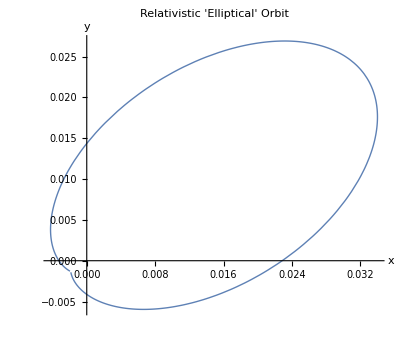

```mathematica
PolarPlot[r[t],{t,3.7940322175405243,10.002448573515926},PlotLabel->"Relativistic 'Elliptical' Orbit",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Solve[ωVal*(10.66+t)/2-2*Pi==0,t]
```

{{t→16.933}}

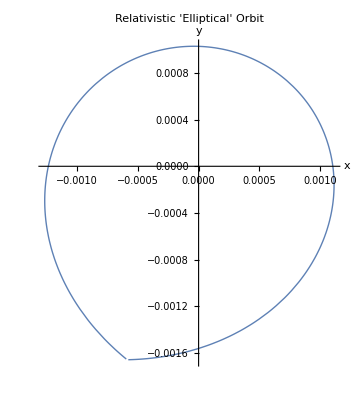

```mathematica
PolarPlot[r[t],{t,10.66, 16.9329615821129},PlotLabel->"Relativistic 'Elliptical' Orbit",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
r[16.932961582112902]-r[10.660000000000002]
```

1.51788×10^-18

```mathematica
16.932961582112902/10.660000000000002
```

1.58846

```mathematica
FindRoot[r[1.588457934532167*t]-r[t]==0,{t,10}]
```

{t→10.66}

```mathematica
1.588457934532167*10.66
```

16.933

```mathematica
r[16.9329615821129]-r[10.660000000000002]
```

-8.67362×10^-19

```mathematica
16.9329615821129/10.660000000000002
```

1.58846

```mathematica
FindRoot[r[1.5884579345321665*t]-r[t]==0,{t,10.6}]
```

{t→10.66}

```mathematica
1.5884579345321665*10.660000000000002
```

16.933

```mathematica
r[16.9329615821129]-r[10.660000000000002]
```

-8.67362×10^-19

```mathematica
{r[16.9329615821129],r[10.660000000000002]}
```

{0.0017562,0.0017562}